## Naloga 1

```mathematica
izraz= (x^5 - 2 * x^2 + 3 * x + 4)/ (x^5 - 2 * x - 1)
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

```mathematica
ReplaceAll[izraz, x-> 1]
```

-3

```mathematica
ReplaceAll[izraz, x-> 2]
```

34/27

```mathematica
ReplaceAll[izraz, x-> 3]
```

119/118

```mathematica
izraz /. x-> 4
```

144/145

ne piši v isto škatlo vec vrednosti, vsakega x-a moras posebaj zapakirat

```mathematica
izraz /. {{x-> 1}, {x-> 2},{x-> 3},{x-> 4}}
```

{-3,34/27,119/118,144/145}

```mathematica
Table[izraz, {x, 1, 10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
f[x_] := (x^5 - 2 * x^2 + 3 * x + 4)/ (x^5 - 2 * x - 1)
```

```mathematica
vrednosti = {1, 2, 3, 4}
```

{1,2,3,4}

```mathematica
Map[f, vrednosti]
```

{-3,34/27,119/118,144/145}

## Naloga 2

```mathematica
sez= Table[10 * i, {i,1,7}]
```

{10,20,30,40,50,60,70}

```mathematica
sez
```

{10,20,30,40,50,60,70}

```mathematica
sez[[3]]
```

30

```mathematica
Take[sez, {1,3}]
```

{10,20,30}

```mathematica
Drop[sez, {2,3}]
```

{10,40,50,60,70}

```mathematica
Part[sez, {1, 3, 5}]
```

{10,30,50}

```mathematica
Take[sez, {-2, -1}]
```

{60,70}

```mathematica
Take[sez, {6,7}]
```

{60,70}

```mathematica
Take[sez, {2,4}]
```

{20,30,40}

```mathematica
Part[sez, {2, 3, 5}]
```

{20,30,50}

```mathematica
Drop[sez, {4, 5}]
```

{10,20,30,60,70}

## Naloga 3

```mathematica
ClearAll[x, a, sez]
```

```mathematica
sez = {x^6, x^2, a}
```

{x^6,x^2,a}

```mathematica
sez /. x-> 3
```

{729,9,a}

```mathematica
sez /. x-> x^2
```

{x^12,x^4,a}

```mathematica
sez /. {x-> 1, x-> 2, x->3}
```

{1,1,a}

```mathematica
sez /. {x->3, a->x}
```

{729,9,x}

```mathematica
ReplaceRepeated[sez, {x-> 3, a-> x}]
```

{729,9,3}

```mathematica
sez //. {x->3, a->x}
```

{729,9,3}

```mathematica
{sez /. x-> 1, sez /. x-> 2,sez /. x-> 3}
```

{{1,1,a},{64,4,a},{729,9,a}}

```mathematica
Table[sez/. x->i, {i,1,10}]
```

{{1,1,a},{64,4,a},{729,9,a},{4096,16,a},{15625,25,a},{46656,36,a},{117649,49,a},{262144,64,a},{531441,81,a},{1000000,100,a}}

## Naloga 4

```mathematica
izraz1= x^5 + 4x^3 - 9
```

-9+4 x^3+x^5

```mathematica
D[izraz1, x]
```

12 x^2+5 x^4

```mathematica
D[izraz1, x]/. x->1
```

17

```mathematica
D[izraz1, x]/. x->5
```

3425

```mathematica
izraz3 = Abs[x + 1]
```

Abs[1+x]

```mathematica
D[izraz3, x]
```

Abs'[1+x]

```mathematica
FullSimplify[D[izraz3, x], x≠ -1 && x ⅇ Reals]
```

Abs'[1+x]

```mathematica
ClearAll[a, x, b]
```

```mathematica
izraz4 = a * x^2 + 3 * b
```

3 b+a x^2

```mathematica
D[izraz4, x]
```

2 a x

```mathematica
2 * a * x/. {{x ->  1}, {x-> 2}}
```

{2 a,4 a}

## Naloga 5

```mathematica
f[x_] := x^3 * Log[4x + 5]
```

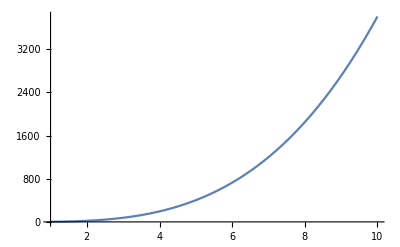

```mathematica
Plot[f[x], {x, 1, 10}]
```

```mathematica
x0 = 5
```

```mathematica
5
```

5

```mathematica
f[x0]
```

```mathematica
125 Log[25]
```

125 Log[25]

```mathematica
k0 =D[f[x], x] /. x -> x0
```

20+75 Log[25]

```mathematica
y = k0 * x + n /. {x-> x0, y-> f[x0]}
```

n+5 (20+75 Log[25])

```mathematica
n0 = n /. resitev // First
```

n

```mathematica
enacba = f[x0] == k0  x0 + n
```

True

```mathematica
resitev = Solve[enacba, n]
```

{{}}

```mathematica
narisi[f_, x0_, x_, zac_, kon_] :=
Module[{k0, n, enacba}, 
k0 = D[f[x], x] /. x-> x0;
enacba = f[x0] == k0 x0 + n;
resitev = Solve[enacba, n];
n0 = n /. resitev // First;
Plot[{f[x], k0 x + n0}, {x, zac, kon}]
]
```

```mathematica
g[x_] := (E^x - x^2) / (Sin[x] - x ^3)
```

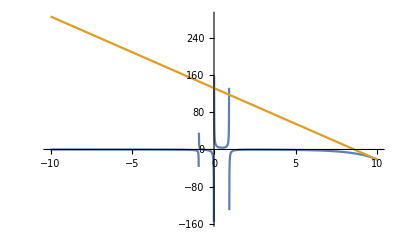

```mathematica
narisi[g, 10, x, -10, 10]
```

## Naloga 6

```mathematica
ClearAll[x, a]
```

```mathematica
Limit[((x^3 - 4 * x^2 + 2 * x + 4) / (x^5 - 9 * x - 14)), x-> 2]
```

-2/71

```mathematica
Limit[((ArcTan[7x]) / (ArcSin[8x])), x-> 0]
```

7/8

```mathematica
Limit[(x^2 - 25) * Cot[π *x], x-> 5]
```

10/π

```mathematica
Limit[(1 + Cos[x]) / (2 * Sqrt[π * x] - π  - x), x-> π ]
```

-2 π

```mathematica
Limit[(Abs[x] * Cot[x]), x-> 0]
```

Indeterminate

Indeterminate

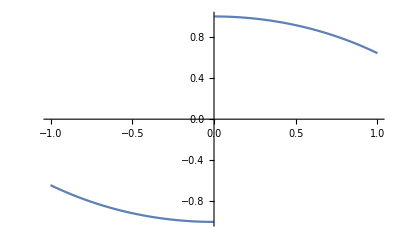

```mathematica
Plot[(Abs[x] * Cot[x]), {x, -1, 1}]
```

```mathematica
Limit[(Abs[x] * Cot[x]), x-> 0, Direction -> FromAbove]
```

1

Plot::optx: Unknown option Direction→FromAbove in Plot[Abs[x] Cot[x],{x,-1,1},Direction→FromAbove].

Plot[Abs[x] Cot[x],{x,-1,1},Direction→FromAbove]

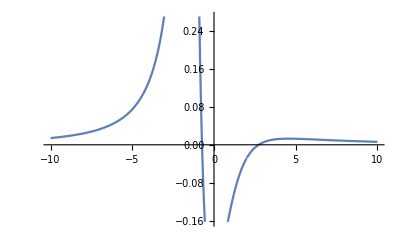

```mathematica
Plot[((x^3 - 4 * x^2 + 2 * x + 4) / (x^5 - 9 * x - 14)), {x,-10,10}]
```

## Naloga 7

```mathematica
ClearAll[x,y,f]
```

```mathematica
f[x_] := (x^2 - 1) / (x^2 - 4)
```

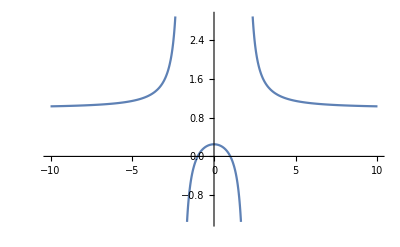

```mathematica
Plot[f[x], {x, -10, 10}]
```

Ničle
Ničle izračunamo tako, da rešimo enačbo f(x) = 0.

```mathematica
Solve[f[x] ==  0, x]
```

{{x→-1},{x→1}}

Funkcija ima ničle v točkah - 1 in 1.

#### Poli

Pole izračunamo, kot ničle imenovalca.

```mathematica
Solve[1/f[x] == 0, x]
```

{{x→-2},{x→2}}

```mathematica
Limit[f[x], x-> 2, Direction -> FromAbove]
```

∞

```mathematica
Limit[f[x], x-> 2, Direction -> FromBelow]
```

-∞

```mathematica
D[f[x], x]
```

(2 x)/(-4+x^2)-(2 x (-1+x^2))/((-4+x^2)^2)

```mathematica
odvod2 = D[f[x], {x, 2}]
```

-(8 x^2)/((-4+x^2)^2)+2/(-4+x^2)+(-1+x^2) ((8 x^2)/((-4+x^2)^3)-2/((-4+x^2)^2))

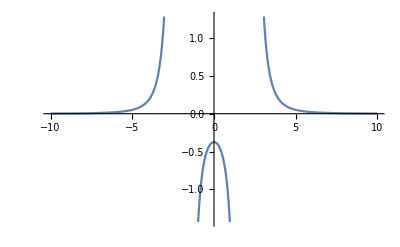

```mathematica
Plot[odvod2, {x, -10, 10}]
```

```mathematica
Reduce[odvod2 > 0, x]
```

x<-2||x>2

## Naloga 8

```mathematica
ClearAll[x]
```

```mathematica
Solve[{x^4 + x^3 - x == 0, x>0} , x] // N
(x /. Solve[{x^4 + x^3 - x == 0, x>0} , x] // First)^2 //N
Reduce[x^4 + x^3 - x == 0 && x>0, x]
```

{{x→0.754878}}

0.56984

x==Root0.755Root[-1+#1^2+#1^3&,1]0.7548776662466927

## Naloga 9

```mathematica
enacba1 = 3 * x^2 - 5 * y^2 == 5
enacba2 = 2  * x^2 + 3 * y^2 == 59
```

3 x^2-5 y^2==5

2 x^2+3 y^2==59

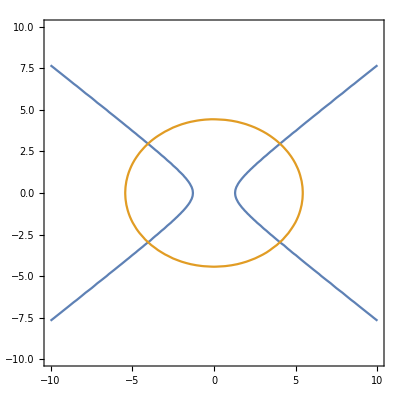

```mathematica
ContourPlot[{3 * x^2 - 5 * y^2 == 5, 2  * x^2 + 3 * y^2 == 59 }, {x, -10, 10}, {y, -10, 10}]
```

```mathematica
ClearAll[x0]
```

```mathematica
Solve[{3 * x^2 - 5 * y^2 == 5, 2  * x^2 + 3 * y^2 == 59} , {x, y}] // N
```

{{x→-4.03928,y→-2.9647},{x→-4.03928,y→2.9647},{x→4.03928,y→-2.9647},{x→4.03928,y→2.9647}}

```mathematica
x0 =
 x/. Solve[{3 * x^2 - 5 * y^2 == 5, 2  * x^2 + 3 * y^2 == 59, x > 0, y > 0} , {x, y}] // First
```

√(310/19)

x0

```mathematica
f1 = y/. Solve[{3 * x^2 - 5 * y^2 == 5, x > 0, y > 0}, y] // First
```

ConditionalExpression[(√(-5+3 x^2))/(√5),x>√(5/3)]

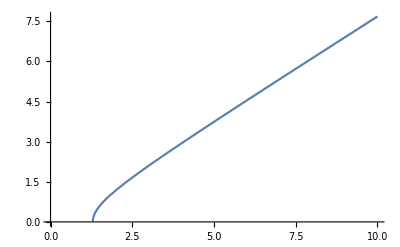

```mathematica
Plot[f1, {x, 0, 10}]
```

```mathematica
f2 = y/. Solve[{2  * x^2 + 3 * y^2 == 59,  x > 0, y > 0}, y] // First
```

ConditionalExpression[(√(59-2 x^2))/(√3),0<x<√(59/2)]

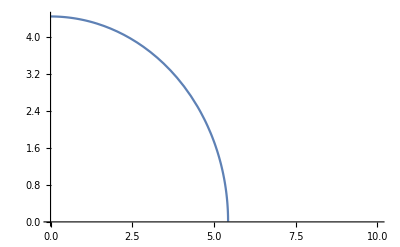

```mathematica
Plot[f2, {x, 0, 10}]
```

```mathematica
k1 = D[f1, x] /. x -> x0
k2 = D[f2, x] /. x -> x0
```

3 √(62/835)

-(2 √(310/167))/3

```mathematica
kot = Abs[ArcTan[k1] - ArcTan[k2]] // N
```

1.42269

```mathematica
57 Degree // N
```

0.994838

```mathematica
kot / Degree
```

81.5141